## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"];
SetDirectory@NotebookDirectory[];
```

```mathematica
GetZFileBCP[𝓈_Integer?NonPositive,ℓ_Integer?NonNegative,𝓂_Integer]:=StringRiffle[{"Data/","Z-Brito-Cardoso-Pani/","sigma_VS_om_a_","s",-Abs@𝓈,"l",ℓ,"m",𝓂,".dat"},""]/;ℓ≥Max[Abs@𝓈,Abs@𝓂];
GetZFile[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer]:="Data/"<>StringRiffle[{"Z",𝓈,ℓ,𝓂},"_"]<>".csv"/;ℓ≥ Max[Abs@𝓈,Abs@𝓂];
```

## Import data

```mathematica
RawDataBCP=Import@GetZFileBCP[-1,1,1];
RawData0=Import@GetZFile[1,1,1];
RawData2=Import@GetZFile[-1,1,1];
ZBCP=DeleteCases[#,{ω_,Z_}/;ω>0.55]&/@GroupBy[{#1,#2 (1+√(1-#1^2)),#3}&@@@MapAt[N@Round[#,10^-3]&,RawDataBCP,{All,1}],First->(Drop[#,1]&)];
Z0=DeleteCases[#,{ω_,Z_}/;ω>0.55]&/@GroupBy[RawData0,First->(Drop[#,1]&)];
Z2=DeleteCases[#,{ω_,Z_}/;ω>0.55]&/@GroupBy[RawData2,First->(Drop[#,1]&)];
```

## Compare values with Brito et al. data

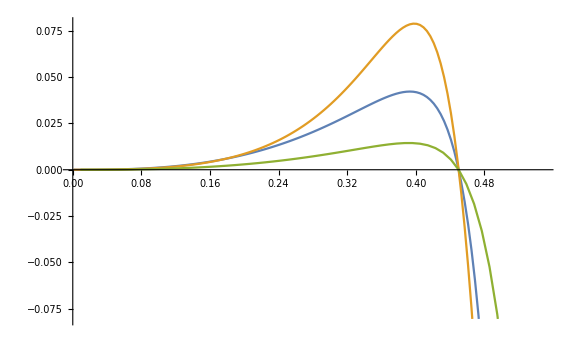

```mathematica
ListPlot[{Z0[0.9],Z2[0.9],ZBCP[0.9]},Joined->True,ImageSize->Large]
```